```mathematica
eqScTo=(ⅇ^(rs/RS-1)==(r/RS-1)ⅇ^(r/RS-1)&&ts==t);
slToSc=FullSimplify[Solve[eqScTo,{rs,ts}]/.C[1]->0,Assumptions->r>RS&&RS>0][[1]]
%//TraditionalForm
slScTo=FullSimplify[Solve[eqScTo,{r,t}]][[1]]
%//TraditionalForm
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{rs→r+RS Log[-1+r/RS],ts→t}

{rs→RS log(r/RS-1)+r,ts→t}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{r→RS (1+ProductLog[ⅇ^(-1+rs/RS)]),t→ts}

{r→RS (W(ⅇ^(rs/RS-1))+1),t→ts}

```mathematica
eqToTl=u==ts-rs&&v==ts+rs;
slTlTo=FullSimplify[Solve[eqToTl,{u,v}]][[1]]
slToTl=FullSimplify[Solve[eqToTl,{ts,rs}]][[1]]
```

{u→-rs+ts,v→rs+ts}

{ts→(u+v)/2,rs→1/2 (-u+v)}

```mathematica
eqKlTl=U==-RS ⅇ^(-u/(2RS))&&V==RS ⅇ^(+v/(2RS));
slKlTl=FullSimplify[Solve[eqKlTl,{U,V}]][[1]]
slTlKl=FullSimplify[Solve[eqKlTl,{u,v}]/.{C[1]->0,C[2]->0}][[1]]
```

{U→-ⅇ^(-u/(2 RS)) RS,V→ⅇ^(v/(2 RS)) RS}

{u→-2 RS Log[-U/RS],v→2 RS Log[V/RS]}

```mathematica
eqKsKl=U==T-R&&V==T+R;
slKsKl=FullSimplify[Solve[eqKsKl,{T,R}]][[1]]
slKlKs=FullSimplify[Solve[eqKsKl,{U,V}]][[1]]
```

{T→(U+V)/2,R→1/2 (-U+V)}

{U→-R+T,V→R+T}

```mathematica
eqClKl=μ==ArcTan[U/RS]&&ν==ArcTan[V/RS];
rgClN=-π/2<μ<π/2&&-π/2<ν<π/2;
slClKl=FullSimplify[Solve[eqClKl,{μ,ν}]][[1]]
slKlCl=FullSimplify[Solve[eqClKl,{U,V}],Assumptions->rgClN][[1]]
```

{μ→ArcTan[U/RS],ν→ArcTan[V/RS]}

{U→RS Tan[μ],V→RS Tan[ν]}

```mathematica
eqCfCl=μ==τ-ρ&&ν==τ+ρ;
slCfCl=FullSimplify[Solve[eqCfCl,{ρ,τ}]][[1]]
slClCf=FullSimplify[Solve[eqCfCl,{μ,ν}]][[1]]
rgCfN=FullSimplify[rgClN/.slClCf]
```

{ρ→1/2 (-μ+ν),τ→(μ+ν)/2}

{μ→-ρ+τ,ν→ρ+τ}

-π/2<-ρ+τ<π/2&&-π/2<ρ+τ<π/2

```mathematica
slTlSc=FullSimplify[slTlTo/.slToSc]
slScTl=FullSimplify[slScTo/.slToTl]
slKlSc=FullSimplify[slKlTl/.slTlSc]
slScKl=FullSimplify[slScTl/.slTlKl]
```

{u→-r+t-RS Log[-1+r/RS],v→r+t+RS Log[-1+r/RS]}

{r→RS (1+ProductLog[ⅇ^(-1+(-u+v)/(2 RS))]),t→(u+v)/2}

{U→-ⅇ^((r-t+RS Log[-1+r/RS])/(2 RS)) RS,V→ⅇ^((r+t+RS Log[-1+r/RS])/(2 RS)) RS}

{r→RS (1+ProductLog[-(U V)/(ⅇ RS^2)]),t→RS (-Log[-U/RS]+Log[V/RS])}

```mathematica
FullSimplify[ⅇ^((RS Log[-1+r/RS])/(2 RS)),Assumptions->(-1+r/RS)>0]
```

√(-1+r/RS)

{T→ⅇ^(r/(2 RS)) √(-1+r/RS) RS Sinh[t/(2 RS)],R→ⅇ^(r/(2 RS)) √(-1+r/RS) RS Cosh[t/(2 RS)]}

ⅇ^(r/RS) RS (-r+RS)

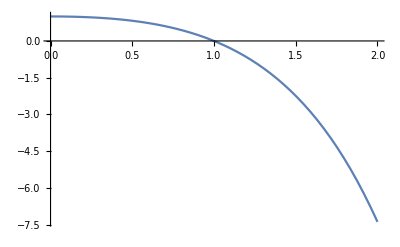

-R^2+T^2<RS^2

{r→RS (1+ProductLog[((R-T) (R+T))/(ⅇ RS^2)]),t→RS (-Log[R-T]+Log[R+T])}

```mathematica
slKsSc=FullSimplify[ExpToTrig[FullSimplify[slKsKl/.slKlSc,Assumptions->t∈Reals&&r>RS&&r>0&&RS>0]]]
FullSimplify[T^2-R^2/.%]
Plot[%/.RS->1,{r,0,2}]
rgKs=T^2-R^2<FullSimplify[(T^2-R^2/.slKsSc)/.r->0]
slScKs=FullSimplify[slScKl/.slKlKs,Assumptions->rgKs&&RS>0]
```

```mathematica
slToKl=FullSimplify[slToTl/.slTlKl]
slKlTo=FullSimplify[slKlTl/.slTlTo]
slToKs=FullSimplify[slToKl/.slKlKs]
slKsTo=Collect[Expand[slKsKl/.slKlTo],RS/2]
```

{ts→RS (-Log[-U/RS]+Log[V/RS]),rs→RS (Log[-U/RS]+Log[V/RS])}

{U→-ⅇ^((rs-ts)/(2 RS)) RS,V→ⅇ^((rs+ts)/(2 RS)) RS}

{ts→RS (-Log[(R-T)/RS]+Log[(R+T)/RS]),rs→RS (Log[(R-T)/RS]+Log[(R+T)/RS])}

{T→-1/2 ⅇ^((rs-ts)/(2 RS)) RS+1/2 ⅇ^((rs+ts)/(2 RS)) RS,R→1/2 (ⅇ^((rs-ts)/(2 RS))+ⅇ^((rs+ts)/(2 RS))) RS}

```mathematica
slTlKs=FullSimplify[slTlKl/.slKlKs]
slKsTl=Collect[Expand[slKsKl/.slKlTl],RS/2]
```

{u→-2 RS Log[(R-T)/RS],v→2 RS Log[(R+T)/RS]}

{T→-1/2 ⅇ^(-u/(2 RS)) RS+1/2 ⅇ^(v/(2 RS)) RS,R→1/2 (ⅇ^(-u/(2 RS))+ⅇ^(v/(2 RS))) RS}

{ρ→1/2 (-ArcTan[U/RS]+ArcTan[V/RS]),τ→1/2 (ArcTan[U/RS]+ArcTan[V/RS])}

{U→-RS Tan[ρ-τ],V→RS Tan[ρ+τ]}

{ρ→1/2 (ArcTan[(R-T)/RS]+ArcTan[(R+T)/RS]),τ→1/2 (ArcTan[(-R+T)/RS]+ArcTan[(R+T)/RS])}

{T→(RS Sin[2 τ])/(Cos[2 ρ]+Cos[2 τ]),R→(RS Sin[2 ρ])/(Cos[2 ρ]+Cos[2 τ])}

-π/2<-ρ+τ<π/2&&-π/2<ρ+τ<π/2&&Cos[2 τ] (Cos[2 ρ]+Cos[2 τ])>0

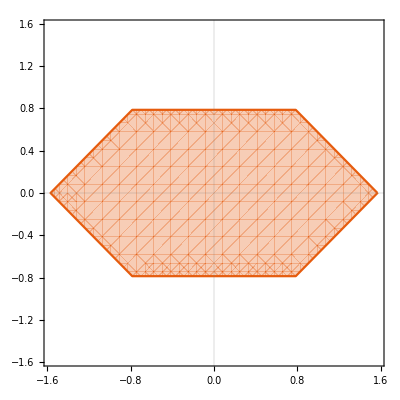

-π/2<-ρ+τ<π/2&&-π/2<ρ+τ<π/2&&-π/4<τ<π/4

```mathematica
slCfKl=FullSimplify[slCfCl/.slClKl]
slKlCf=FullSimplify[slKlCl/.slClCf]
slCfKs=FullSimplify[slCfKl/.slKlKs]
slKsCf=FullSimplify[slKsKl/.slKlCf]
rgCf=rgCfN&&FullSimplify[(rgKs/.slKsCf),Assumptions->RS>0]
RegionPlot[rgCf,{ρ,-π/2,π/2},{τ,-π/2,π/2},AspectRatio->Automatic,PlotTheme->"Scientific"]
rgCf=rgCfN&&-π/4<τ<π/4
```

```mathematica
slCfSc=FullSimplify[slCfKs/.slKsSc]
slScCf=FullSimplify[slScKs/.slKsCf,Assumptions->RS>0&&rgCf]
```

{ρ→1/2 (ArcTan[ⅇ^((r-t)/(2 RS)) √(-1+r/RS)]+ArcTan[ⅇ^((r+t)/(2 RS)) √(-1+r/RS)]),τ→1/2 (-ArcTan[ⅇ^((r-t)/(2 RS)) √(-1+r/RS)]+ArcTan[ⅇ^((r+t)/(2 RS)) √(-1+r/RS)])}

{r→RS (1+ProductLog[(1-(2 Cos[2 ρ])/(Cos[2 ρ]+Cos[2 τ]))/ⅇ]),t→RS (-Log[Tan[ρ-τ]]+Log[Tan[ρ+τ]])}

```mathematica
slCfTo=FullSimplify[slCfKs/.slKsTo]
%//TraditionalForm
slToCf=FullSimplify[slToKs/.slKsCf]
```

{ρ→1/4 (π+Gudermannian[(rs-ts)/(2 RS)]+Gudermannian[(rs+ts)/(2 RS)]),τ→1/4 (-Gudermannian[(rs-ts)/(2 RS)]+Gudermannian[(rs+ts)/(2 RS)])}

{ρ→1/4 (gd((rs-ts)/(2 RS))+gd((rs+ts)/(2 RS))+π),τ→1/4 (gd((rs+ts)/(2 RS))-gd((rs-ts)/(2 RS)))}

{ts→RS (-Log[Tan[ρ-τ]]+Log[Tan[ρ+τ]]),rs→RS (Log[Tan[ρ-τ]]+Log[Tan[ρ+τ]])}

```mathematica
slCfTl=FullSimplify[slCfKs/.slKsTl]
%//TraditionalForm
slTlCf=FullSimplify[slTlKs/.slKsCf]
```

{ρ→1/4 (π+Gudermannian[-u/(2 RS)]+Gudermannian[v/(2 RS)]),τ→1/4 (-Gudermannian[-u/(2 RS)]+Gudermannian[v/(2 RS)])}

{ρ→1/4 (gd(-u/(2 RS))+gd(v/(2 RS))+π),τ→1/4 (gd(v/(2 RS))-gd(-u/(2 RS)))}

{u→-2 RS Log[Tan[ρ-τ]],v→2 RS Log[Tan[ρ+τ]]}

```mathematica
(*∂_t *)
pdtKs=FullSimplify[TrigToExp[FullSimplify[ReleaseHold[Hold[{D[R, t],D[T, t]}]/.slKsSc]/.slScKs]],Assumptions->R>T&&R>0&&T>0&&RS>0]
pdrKs=FullSimplify[TrigToExp[FullSimplify[ReleaseHold[Hold[{D[R, r],D[T, r]}]/.slKsSc]/.slScKs]],Assumptions->R>T&&R>0&&T>0&&RS>0]
pdrsKs=FullSimplify[TrigToExp[FullSimplify[ReleaseHold[Hold[{D[R, rs],D[T, rs]}]/.slKsTo]/.slToKs]],Assumptions->R>T&&R>0&&T>0&&RS>0]
pduKs=FullSimplify[TrigToExp[FullSimplify[ReleaseHold[Hold[{D[R, u],D[T, u]}]/.slKsTl]/.slTlKs]],Assumptions->R>T&&R>0&&T>0&&RS>0]
pdvKs=FullSimplify[TrigToExp[FullSimplify[ReleaseHold[Hold[{D[R, v],D[T, v]}]/.slKsTl]/.slTlKs]],Assumptions->R>T&&R>0&&T>0&&RS>0]
```

{T/(2 RS),R/(2 RS)}

{(R (1+1/ProductLog[((R-T) (R+T))/(ⅇ RS^2)]))/(2 RS),(T (1+1/ProductLog[((R-T) (R+T))/(ⅇ RS^2)]))/(2 RS)}

{R/(2 RS),T/(2 RS)}

{(-R+T)/(4 RS),(R-T)/(4 RS)}

{(R+T)/(4 RS),(R+T)/(4 RS)}

```mathematica
pdUKs=FullSimplify[ReleaseHold[Hold[{D[R, U],D[T, U]}]/.slKsKl]/.slKlKs]
```

{-1/2,1/2}

```mathematica
pdtCf=FullSimplify[ReleaseHold[Hold[{D[ρ, t],D[τ, t]}]/.slCfSc]/.slScCf]
pdrsCf=FullSimplify[ReleaseHold[Hold[{D[ρ, rs],D[τ, rs]}]/.slCfTo]/.slToCf]
pduCf=FullSimplify[ReleaseHold[Hold[{D[ρ, u],D[τ, u]}]/.slCfTl]/.slTlCf]
pdvCf=FullSimplify[ReleaseHold[Hold[{D[ρ, v],D[τ, v]}]/.slCfTl]/.slTlCf]
```

{(Cos[2 ρ] Sin[2 τ] √Tan[ρ-τ] √Tan[ρ+τ])/(4 RS √(1-(2 Cos[2 ρ])/(Cos[2 ρ]+Cos[2 τ]))),(Cos[2 τ] Sin[2 ρ] √Tan[ρ-τ] √Tan[ρ+τ])/(4 RS √(1-(2 Cos[2 ρ])/(Cos[2 ρ]+Cos[2 τ])))}

{(Cos[2 τ] Sin[2 ρ])/(4 RS),(Cos[2 ρ] Sin[2 τ])/(4 RS)}

{-Sin[2 (ρ-τ)]/(8 RS),Sin[2 (ρ-τ)]/(8 RS)}

{Sin[2 (ρ+τ)]/(8 RS),Sin[2 (ρ+τ)]/(8 RS)}

```mathematica
FullSimplify[(1+ProductLog[(1-(2 Cos[2 ρ])/(Cos[2 ρ]+Cos[2 τ]))/ⅇ])FullSimplify[ReleaseHold[Hold[{D[ρ, r],D[τ, r]}]/.slCfSc]/.slScCf]]/(1+ProductLog[(1-(2 Cos[2 ρ])/(Cos[2 ρ]+Cos[2 τ]))/ⅇ])
pdrCf=%;
```

{(Cos[2 τ] √(1-(2 Cos[2 ρ])/(Cos[2 ρ]+Cos[2 τ])) (1+ProductLog[(1-(2 Cos[2 ρ])/(Cos[2 ρ]+Cos[2 τ]))/ⅇ]) Sin[2 ρ])/(4 RS ProductLog[(1-(2 Cos[2 ρ])/(Cos[2 ρ]+Cos[2 τ]))/ⅇ] √Tan[ρ-τ] √Tan[ρ+τ]),(Cos[2 ρ] √(1-(2 Cos[2 ρ])/(Cos[2 ρ]+Cos[2 τ])) (1+ProductLog[(1-(2 Cos[2 ρ])/(Cos[2 ρ]+Cos[2 τ]))/ⅇ]) Sin[2 τ])/(4 RS ProductLog[(1-(2 Cos[2 ρ])/(Cos[2 ρ]+Cos[2 τ]))/ⅇ] √Tan[ρ-τ] √Tan[ρ+τ])}

```mathematica
pdTCf=FullSimplify[ReleaseHold[Hold[{D[ρ, T],D[τ, T]}]/.slCfKs]/.slKsCf]
pdUCf=FullSimplify[ReleaseHold[Hold[{D[ρ, U],D[τ, U]}]/.slCfKl]/.slKlCf]
pdVCf=FullSimplify[ReleaseHold[Hold[{D[ρ, V],D[τ, V]}]/.slCfKl]/.slKlCf]
```

{-(2 Cos[ρ] Cos[τ] Sin[ρ] Sin[τ])/RS,(1+Cos[2 ρ] Cos[2 τ])/(2 RS)}

{-Cos[ρ-τ]^2/(2 RS),Cos[ρ-τ]^2/(2 RS)}

{Cos[ρ+τ]^2/(2 RS),Cos[ρ+τ]^2/(2 RS)}

```mathematica
ProductLog[x] ⅇ^ProductLog[x]//FullSimplify
```

x